```mathematica
ϵ[m_]=If[m==0, -s kappa, Sign[m]Sqrt[Abs[m]+ kappa^2]];
alpha[m_]=(-Sqrt[Abs[m]])/(ϵ[m] s - kappa);
xi=((alpha[m]^2+1)(alpha[n]^2+1))^(-1)/(ϵ[m]-ϵ[n])^2; (*Nb defined without heaviside *)
```

```mathematica
Integrate[
xi (ϵ[m] + ϵ[n]) alpha[m]^2/.{n->0, m->1,s->1},
{kappa,  0, Infinity}
]
```

1/4

```mathematica
Table[
Integrate[
xi (ϵ[m] + ϵ[n]) alpha[m]^2/.{n->-i, m->i+1,s->1},
{kappa,  -Infinity, Infinity}
],
{i, 1,2}
]
```

```mathematica
FullSimplify[xi (ϵ[m] + ϵ[n]) alpha[m]^2/.s->1, {m>0, n<0, {m,n}∈Reals}]
```

(m (√(kappa^2+m)-√(kappa^2+Abs[n])) (kappa+√(kappa^2+Abs[n]))^2)/(4 (kappa^2+m-kappa √(kappa^2+m)) (√(kappa^2+m)+√(kappa^2+Abs[n]))^2 (Abs[n]+kappa (kappa+√(kappa^2+Abs[n]))))

```mathematica
Integrate[
(m (√(kappa^2+m)-√(kappa^2-n)) (kappa+√(kappa^2-n))^2)/(4 (kappa^2+m-kappa √(kappa^2+m)) (√(kappa^2+m)+√(kappa^2-n))^2 (-n+kappa (kappa+√(kappa^2-n)))),
{kappa, -Infinity, Infinity},
Assumptions->{{m,n}∈Integers, m>0, n<0}
]
```

(m^2-n^2+2 m n Log[-m/n])/(4 (m+n)^2)

```mathematica
%/.{m->i+1, n->-i}
```

1/4 (-i^2+(1+i)^2-2 i (1+i) Log[(1+i)/i])

```mathematica
Simplify[%]
```

1/4 (1+2 i-2 i (1+i) Log[1+1/i])

```mathematica
Sum[1/4 (1+2 i-2 i (1+i) Log[1+1/i]), {i, N}, GenerateConditions->True]
```

ConditionalExpression[1/12 (-1+6 N+3 N^2+12 Log[Glaisher]+6 Zeta^(1,0)[-2,1+N]-6 Zeta^(1,0)[-2,2+N]+6 Zeta^(1,0)[-1,1+N]+6 Zeta^(1,0)[-1,2+N]), N∈ℤ&&N≥1]

We have from https : // functions . wolfram . com/ZetaFunctionsandPolylogarithms/Zeta2/20/01/01/01/03/0002/

```mathematica
Derivative[1,0][Zeta][-1,a]==PolyGamma[-2,a-1]-(1/12) (-13+18 a-6 a^2-12 (-1+a) Log[-1+a]+12 Log[Glaisher]+6 (-1+a) Log[2 Pi])+UnitStep[Floor[-Re[a]]] Sum[(a+i) Log[a+i]-(1/2) ((a+i)^2)^(1/2) Log[(a+i)^2],{i,0,Floor[-Re[a]]}]
```

```mathematica
Derivative[1,0][Zeta][-2,a]==(1/(12 Pi^2)) (2 (-9+a (18+3 a (-6+EulerGamma)+EulerGamma+2 a^2 EulerGamma)) Pi^2-3 Zeta[3]+Pi^2 ((1+6 a (1+a)) (-3+2 EulerGamma) Floor[-Re[a]]+3 (1+2 a) (-3+2 EulerGamma) Floor[-Re[a]]^2+(-6+4 EulerGamma) Floor[-Re[a]]^3+6 ((-1+a) (Log[2]+2 (-1+a) Log[-1+a]-4 Log[Glaisher]+Log[Pi]-a Log[2 Pi])+4 PolyGamma[-3,-1+a]+2 Sum[(1/2) (a+k)^2 (2 Log[a+k]-Log[(a+k)^2]),{k,0,Floor[-Re[a]]}]+(-3+2 EulerGamma) Zeta[-2,a+Max[0,Floor[1-Re[a]]]])))
```

```mathematica
FullSimplify[PolyGamma[-2,a-1]-(1/12) (-13+18 a-6 a^2-12 (-1+a) Log[-1+a]+12 Log[Glaisher]+6 (-1+a) Log[2 Pi])+UnitStep[Floor[-Re[a]]] Sum[(a+i) Log[a+i]-(1/2) ((a+i)^2)^(1/2) Log[(a+i)^2],{i,0,Floor[-Re[a]]}],
Assumptions->{a>=2, a∈Integers}]
```

a Log[-1+a]+1/12 (13-12 Log[(-1+a) Glaisher]+6 a (-3+a-Log[2 π])+6 Log[2 π])+PolyGamma[-2,-1+a]

The other forumla requires a bit more manual massage

```mathematica
FullSimplify[(1/(12 Pi^2)) (2 (-9+a (18+3 a (-6+EulerGamma)+EulerGamma+2 a^2 EulerGamma)) Pi^2-3 Zeta[3]+Pi^2 ((1+6 a (1+a)) (-3+2 EulerGamma) (-a)+3 (1+2 a) (-3+2 EulerGamma) (-a)^2+(-6+4 EulerGamma) (-a)^3+6 ((-1+a) (Log[2]+2 (-1+a) Log[-1+a]-4 Log[Glaisher]+Log[Pi]-a Log[2 Pi])+4 PolyGamma[-3,-1+a]+(-3+2 EulerGamma) Zeta[-2,a]))),
Assumptions->{a>=2, a∈Integers}]
```

(-1+a)^2 Log[-1+a]-1/6 (-1+a) (-9+12 Log[Glaisher]+Log[1/(8 π^3)]+a (12+2 a (-3+EulerGamma)-EulerGamma+Log[8]+3 Log[π]))+2 PolyGamma[-3,-1+a]-Zeta[3]/(4 π^2)

```mathematica
zetasimp={
Derivative[1,0][Zeta][-1,a_]->a Log[-1+a]+1/12 (13-12 Log[(-1+a) Glaisher]+6 a (-3+a-Log[2 π])+6 Log[2 π])+PolyGamma[-2,-1+a],
Derivative[1,0][Zeta][-2,a_]->(-1+a)^2 Log[-1+a]-1/6 (-1+a) (-9+12 Log[Glaisher]+Log[1/(8 π^3)]+a (12+2 a (-3+EulerGamma)-EulerGamma+Log[8]+3 Log[π]))+2 PolyGamma[-3,-1+a]-Zeta[3]/(4 π^2)
};
```

```mathematica
1/12 (-1+6 N+3 N^2+12 Log[Glaisher]+6 Derivative[1,0][Zeta][-2,1+N]-6 Derivative[1,0][Zeta][-2,2+N]+6 Derivative[1,0][Zeta][-1,1+N]+6 Derivative[1,0][Zeta][-1,2+N])/.zetasimp
```

1/12 (-1+6 N+3 N^2+12 Log[Glaisher]+6 ((1+N) Log[N]+1/12 (13-12 Log[Glaisher N]+6 (1+N) (-2+N-Log[2 π])+6 Log[2 π])+PolyGamma[-2,N])+6 ((2+N) Log[1+N]+1/12 (13-12 Log[Glaisher (1+N)]+6 (2+N) (-1+N-Log[2 π])+6 Log[2 π])+PolyGamma[-2,1+N])+6 (N^2 Log[N]-1/6 N (-9+12 Log[Glaisher]+Log[1/(8 π^3)]+(1+N) (12-EulerGamma+2 (-3+EulerGamma) (1+N)+Log[8]+3 Log[π]))+2 PolyGamma[-3,N]-Zeta[3]/(4 π^2))-6 ((1+N)^2 Log[1+N]-1/6 (1+N) (-9+12 Log[Glaisher]+Log[1/(8 π^3)]+(2+N) (12-EulerGamma+2 (-3+EulerGamma) (2+N)+Log[8]+3 Log[π]))+2 PolyGamma[-3,1+N]-Zeta[3]/(4 π^2)))

```mathematica
FullSimplify[%, Assumptions->{N>=1, N∈Integers}]
```

1/4 ((-3+2 EulerGamma) (1+N)^2-2 N (2 N ArcCoth[1+2 N]-2 Log[N]+Log[1+N])+Log[2 Glaisher^4 π])+PolyGamma[-3,N]-PolyGamma[-3,1+N]+PolyGamma[-2,N]

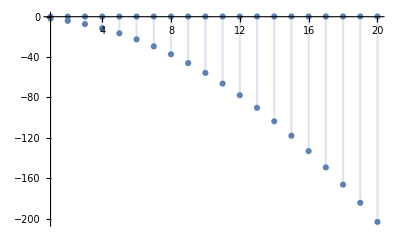

```mathematica
DiscretePlot[{1/12 (-1+6 N+3 N^2+12 Log[Glaisher]+6 Derivative[1,0][Zeta][-2,1+N]-6 Derivative[1,0][Zeta][-2,2+N]+6 Derivative[1,0][Zeta][-1,1+N]+6 Derivative[1,0][Zeta][-1,2+N]),
1/4 ((-3+2 EulerGamma) (1+N)^2-2 N (2 N ArcCoth[1+2 N]-2 Log[N]+Log[1+N])+Log[2 Glaisher^4 π])+PolyGamma[-3,N]-PolyGamma[-3,1+N]+PolyGamma[-2,N]}/.N->k, {k, 20}]
```

```mathematica
Expand[Derivative[1,0][Zeta][-1,a]]
```

Zeta^(1,0)[-1,a]

```mathematica
Derivative[1,0][Zeta][-1,a]
```

Zeta^(1,0)[-1,a]

```mathematica
FullSimplify[1/12 (-1+6 N+3 N^2+12 Log[Glaisher]+6 Derivative[1,0][Zeta][-2,1+N]-6 Derivative[1,0][Zeta][-2,2+N]+6 Derivative[1,0][Zeta][-1,1+N]+6 Derivative[1,0][Zeta][-1,2+N]),
N∈PositiveIntegers]
```

1/12 (-1+3 N (2+N)+12 Log[Glaisher]+6 Zeta^(1,0)[-2,1+N]-6 Zeta^(1,0)[-2,2+N]+6 Zeta^(1,0)[-1,1+N]+6 Zeta^(1,0)[-1,2+N])

```mathematica
TraditionalForm[1/12 (-1+6 N+3 N^2+12 Log[Glaisher]+6 Derivative[1,0][Zeta][-2,1+N]-6 Derivative[1,0][Zeta][-2,2+N]+6 Derivative[1,0][Zeta][-1,1+N]+6 Derivative[1,0][Zeta][-1,2+N])]
```

```mathematica
1/12 (-1+6 N+3 N^2+12 Log[Glaisher]+6 Derivative[1,0][Zeta][-2,1+N]-6 Derivative[1,0][Zeta][-2,2+N]+6 Derivative[1,0][Zeta][-1,1+N]+6 Derivative[1,0][Zeta][-1,2+N])+1/4
```

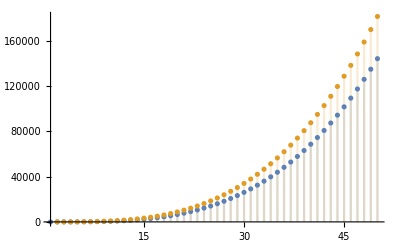

```mathematica
DiscretePlot[
{Derivative[1,0][Zeta][-2,a],(1/(12 Pi^2)) (2 (-9+a (18+3 a (-6+EulerGamma)+EulerGamma+2 a^2 EulerGamma)) Pi^2-3 Zeta[3]+Pi^2 ((1+6 a (1+a)) (-3+2 EulerGamma) Floor[-Re[a]]+3 (1+2 a) (-3+2 EulerGamma) Floor[-Re[a]]^2+(-6+4 EulerGamma) Floor[-Re[a]]^3+6 ((-1+a) (Log[2]+2 (-1+a) Log[-1+a]-4 Log[Glaisher]+Log[Pi]-a Log[2 Pi])+4 PolyGamma[-3,-1+a]+2 Sum[(1/2) (a+k)^2 (2 Log[a+k]-Log[(a+k)^2]),{k,0,Floor[-Re[a]]}]+(-3+2 EulerGamma) Zeta[-2,a+Max[0,Floor[1-Re[a]]]])))},
{a,1,50}]
```

```mathematica
TeXForm[%]
```

\frac{1}{12} \left(6 \zeta ^{(1,0)}(-2,N+1)-6
   \zeta ^{(1,0)}(-2,N+2)+6 \zeta
   ^{(1,0)}(-1,N+1)+6 \zeta
   ^{(1,0)}(-1,N+2)+12 \log (A)+3 N^2+6
   N-1\right)

```mathematica
TraditionalForm[1/4 (1+2 i-2 i (1+i) Log[1+1/i])]
```

1/4 (2 i-2 (i+1) i log(1/i+1)+1)

```mathematica
1/4 (1+2 i-2 i (1+i) Log[1+1/i])/.i->1
```

1/4 (3-4 Log[2])

```mathematica
FullSimplify[(1+2 i-2 i (1+i) Log[1+1/i]), Assumptions->i∈PositiveIntegers]
```

1+2 i-2 i (1+i) Log[1+1/i]

```mathematica
Sum[(1+2 i-2 i (1+i) Log[1+1/i]), {i, 1,N}, Assumptions->i∈PositiveReals]
```

1/3 (-1+6 N+3 N^2+12 Log[Glaisher]+6 Zeta^(1,0)[-2,1+N]-6 Zeta^(1,0)[-2,2+N]+6 Zeta^(1,0)[-1,1+N]+6 Zeta^(1,0)[-1,2+N])

```mathematica
Simplify[%%]
```

1-2 (-1+Log[1/i]) i-2 (1+Log[1/i]) i^2-i^3+O[i]^4

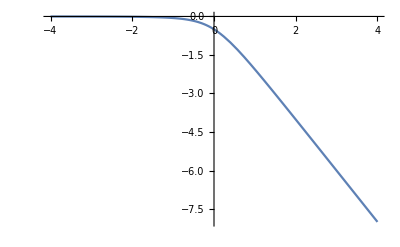

```mathematica
Plot[
xi (ϵ[m] + ϵ[n]) alpha[m]^2/.{n->0, m->-1, s->1},
{kappa, -4,4}
]
```

```mathematica
olddat=Import["/home/thorvald/Documents/NTNU/09semester/ProjectThesis/Thesis/figures/convergence_chi2.dat"][[2;;, {1,2}]];
```

```mathematica
2+8 1/12 (-1+6 N+3 N^2+12 Log[Glaisher]+6 Derivative[1,0][Zeta][-2,1+N]-6 Derivative[1,0][Zeta][-2,2+N]+6 Derivative[1,0][Zeta][-1,1+N]+6 Derivative[1,0][Zeta][-1,2+N])
```

```mathematica
Table[{N[2+2/3 (-1+6 i+3 i^2+12 Log[Glaisher]+6 Derivative[1,0][Zeta][-2,1+i]-6 Derivative[1,0][Zeta][-2,2+i]+6 Derivative[1,0][Zeta][-1,1+i]+6 Derivative[1,0][Zeta][-1,2+i])], olddat[[i+1, 2]]},{i,30}]
```

{{2.45482,2.45482},{2.72366,2.72366},{2.91492,2.91492},{3.06344,3.06344},{3.18485,3.18485},{3.28754,3.28754},{3.3765,3.3765},{3.45499,3.45499},{3.5252,3.5252},{3.58872,3.58872},{3.64672,3.64672},{3.70007,3.70007},{3.74946,3.74946},{3.79545,3.79545},{3.83847,3.83847},{3.87888,3.87888},{3.91698,3.91698},{3.95303,3.95303},{3.98722,3.98722},{4.01974,4.01974},{4.05075,4.05075},{4.08039,4.08039},{4.10876,4.10876},{4.13597,4.13597},{4.16212,4.16212},{4.18728,4.18728},{4.21152,4.21152},{4.23491,4.23491},{4.25751,4.25751},{4.27937,4.27937}}

```mathematica
contrib=Table[
4(1/4 + 1/12 (-1+6 n+3 n^2+12 Log[Glaisher]+6 Derivative[1,0][Zeta][-2,1+n]-6 Derivative[1,0][Zeta][-2,2+n]+6 Derivative[1,0][Zeta][-1,1+n]+6 Derivative[1,0][Zeta][-1,2+n]))//N,
{n,0, 300}
];
```

```mathematica
Export["/home/thorvald/Documents/NTNU/10semester/Thesis/data/notilt_contrib.csv", 
MapThread[{#1, #2}&,{Table[n, {n, 0, Length[contrib]-1}], contrib}]
]
```

/home/thorvald/Documents/NTNU/10semester/Thesis/data/notilt_contrib.csv